# OCR for Sheet Music

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Final(?) Data Preprocessing

```mathematica
PreprocessData["datasets/DeepScores","datasets/deepscoresWL-final"]
```

$Aborted

```mathematica
PreprocessData["datasets/DeepScores_Validation","datasets/deepscoresWL-final_Validation"]
```

$Aborted

## Segmentation (ML)

## Loading the Data

We are using the DeepScores dataset:

https://arxiv.org/pdf/1804.00525.pdf

https://apacha.github.io/OMR-Datasets/#deepscores

https://drive.google.com/drive/folders/1KFxqi0rO-bJrd03rLk87fF1iOmnjpaoG)

```mathematica
loadData[path_String?DirectoryQ,n_] := MapThread[Import[#1]->Import[#2]&,
{Take[FileNames[All,FileNameJoin[{path,"images_png"}]],n],Take[FileNames[All,FileNameJoin[{path,"pix_annotations_png"}]],n]}]
```

```mathematica
data=loadData["datasets/DeepScores",30];
```

### Out-of-core version

```mathematica
loadDataOutOfCore[path_String?DirectoryQ] := Flatten[MapThread[File[#⟦1⟧]->File[#⟦2⟧]&/@Thread[{#1,#2}&[FileNames[All,#1],FileNames[All,#2]]]&,
{FileNames[All,FileNameJoin[{path,"images_png"}]],FileNames[All,FileNameJoin[{path,"pix_annotations_png"}]]}],1]
```

```mathematica
outOfCoreData=loadDataOutOfCore["datasets/deepscoresWL"];
```

```mathematica
Take[outOfCoreData,2]
```

{File[datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-4.png/1.png]→File[datasets/deepscoresWL/pix_annotations_png/lg-100016039-aug-beethoven--page-4.png/1.png],File[datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-4.png/2.png]→File[datasets/deepscoresWL/pix_annotations_png/lg-100016039-aug-beethoven--page-4.png/2.png]}

## Checking out the data

```mathematica
assocImport[a_->b_] := Import@a -> Import@b
```

```mathematica
assocImport/@RandomSample[outOfCoreData,5]//TableForm
```

-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-
-Graphics-→-Graphics-

## Preprocessing the Data

### From Markus’ Notebook

```mathematica
imageMax[imgs__Image]:=ImageApply[Max,ColorCombine[{imgs}]];
```

```mathematica
imageMin[imgs__Image]:=ImageApply[Min,ColorCombine[{imgs}]];
```

```mathematica
detectStaffLineImages[image_,segmentized_] := Module[{
staffLines =Select[ImageLines[BottomHatTransform[image,BoxMatrix[{1,0}]],Automatic,0.0065]⟦All,1⟧,(Abs@VectorAngle[Subtract@@#,{-1,0}]<10°)&]
},
Δ =Median@Differences@Sort@Map[Mean,staffLines⟦All,All,2⟧];
staffLineGroups=Gather[Sort[staffLines,(Last@Mean@#1>Last@Mean@#2)&],(Last@Mean@#1-Last@Mean@#2<5Δ)&];
{Map[
ImageTrim[image,Flatten[#,1],{0,4Δ}]&,
staffLineGroups
],Map[
ImageTrim[segmentized,Flatten[#,1],{0,4Δ}]&,
staffLineGroups
],Δ}
]
```

```mathematica
removeStaffLines[image_,Δ_]:=
With[
{withoutStaffLines=imageMin[Closing[image,BoxMatrix[{Δ/6,0}]],ColorNegate@BottomHatTransform[image,BoxMatrix[{0,Δ}]]]},
imageMax[withoutStaffLines,MorphologicalBinarize[withoutStaffLines,{0.66,0.33}]]
]
```

### Preprocessing Function

Since we are doing out-of-core training, we need to Import, process and then Export the images.

```mathematica
adjustDimensions[image_] := ImageResize[image,{2058,512},Resampling->"Nearest"]
```

```mathematica
PreprocessImage[image_,segmentized_] := (
{imgs,segms,Δ}=detectStaffLineImages[image,segmentized];
Thread[({#1,#2}&)[adjustDimensions[removeStaffLines[#,Δ]]&/@imgs,adjustDimensions[ImageApply[(If[#==0,0,Abs[1-#]]&),#]]&/@segms]]
)
```

```mathematica
PreprocessData[inputPath_String?DirectoryQ,outputPath_String?DirectoryQ] :=
Function[{pathImage,pathSegmentized},
If[DirectoryQ[pathImage],
PreprocessData[pathImage,FileNameJoin[{outputPath,FileNameTake[pathImage]}]],
(
CreateDirectory[FileNameJoin[{outputPath,"images_png",FileNameTake[pathImage]}]]//Quiet;
CreateDirectory[FileNameJoin[{outputPath,"pix_annotations_png",FileNameTake[pathSegmentized]}]]//Quiet;
MapIndexed[
(
Export[FileNameJoin[{outputPath,"images_png",FileNameTake[pathImage],ToString[First[#2]]<>".png"}],#1⟦1⟧];
Export[FileNameJoin[{outputPath,"pix_annotations_png",FileNameTake[pathSegmentized],ToString[First[#2]]<>".png"}],#1⟦2⟧]
)&,
PreprocessImage[Import[pathImage],Import[pathSegmentized]]]
)
]
]@@#&/@Thread[{#1,#2}&[FileNames[All,FileNameJoin[{inputPath,"images_png"}]],FileNames[All,FileNameJoin[{inputPath,"pix_annotations_png"}]]]]
```

### Running It

```mathematica
PreprocessData["datasets/DeepScores","datasets/deepscoresWL"]
```

$Aborted

### Resizing it all

```mathematica
ResizeImages[path_] := If[DirectoryQ[#],
ResizeImages[#],
Export[#,ImageResize[Import[#],{512,128},Resampling->"Nearest"]]]&/@FileNames[All,path]
```

```mathematica
ResizeImages["datasets/deepscoresWL-final/images_png"];
```

```mathematica
ResizeImages["datasets/deepscoresWL-final/pix_annotations_png"];
```

```mathematica
ResizeImages["datasets/deepscoresWL-final_Validation/images_png"];
```

```mathematica
ResizeImages["datasets/deepscoresWL-final_Validation/pix_annotations_png"];
```

### Padding the Staff Images

Find the biggest image dimensions

```mathematica
MaxDataWidth[path_] := Module[
{dirs=Select[FileNames[All,path],DirectoryQ]},
files=Complement[FileNames[All,path],dirs];
Max[
If[files≠{},
ImageDimensions[
Import[
First[
MaximalBy[files,ImageDimensions[Import[#]]⟦1⟧&]
]
]
],
{}
],
Max[MaxDataWidth/@dirs]
]
]
```

```mathematica
MaxDataHeight[path_] := Module[
{dirs=Select[FileNames[All,path],DirectoryQ]},
files=Complement[FileNames[All,path],dirs];
Max[
If[files≠{},
ImageDimensions[
Import[
First[
MaximalBy[files,ImageDimensions[Import[#]]⟦2⟧&]
]
]
],
{}
],
Max[MaxDataHeight/@dirs]
]
]
```

Pad all the images in the directory (recursively) to given dimensions

```mathematica
PadData[path_,maxWidth_,maxHeight_] := (fpath↦If[DirectoryQ[fpath],
PadData[fpath,maxWidth,maxHeight],
(
image=Import[fpath];
{width,height}=ImageSize[image];
Export[fpath,ImagePad[image,{{(maxWidth-width)0.5,(maxHeight-height)0.5},{(maxWidth-width)0.5,(maxHeight-height)0.5}}]];
)
])/@FileNames[All,path]
```

```mathematica
maxWidth=MaxDataWidth["datasets/deepscoresWL/images_png"]
```

2984

```mathematica
maxHeight=MaxDataHeight["datasets/deepscoresWL/images_png"]
```

2984

```mathematica
Import["datasets/deepscoresWL/images_png_nopad/lg-100016039-aug-beethoven--page-4.png/3.jpg"]
```

-Graphics-

```mathematica
ImageDimensions[%]
```

{2707,452}

```mathematica
PadData["datasets/deepscoresWL",MaxDataWidth["datasets/deepscoresWL/images_png"]//Echo,MaxDataHeight["datasets/deepscoresWL/images_png"]//Echo]
```

{datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-4.png,datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-7.png,datasets/deepscoresWL/images_png/lg-100016039-aug-emmentaler--page-11.png,datasets/deepscoresWL/images_png/lg-100016039-aug-emmentaler--page-2.png,datasets/deepscoresWL/images_png/lg-100016039-aug-lilyjazz--page-13.png,datasets/deepscoresWL/images_png/lg-100052827-aug-gutenberg1939--page-1.png,datasets/deepscoresWL/images_png/lg-100057130-aug-beethoven--page-10.png,datasets/deepscoresWL/images_png/lg-100057130-aug-beethoven--page-11.png,datasets/deepscoresWL/images_png/lg-100057130-aug-beethoven--page-12.png,datasets/deepscoresWL/images_png/lg-100057130-aug-emmentaler--page-7.png,datasets/deepscoresWL/images_png/lg-100057130-aug-gonville--page-14.png,datasets/deepscoresWL/images_png/lg-100080340-aug-emmentaler--page-8.png,datasets/deepscoresWL/images_png/lg-100080340-aug-gutenberg1939--page-3.png,datasets/deepscoresWL/images_png/lg-100080340-aug-lilyjazz--page-4.png,datasets/deepscoresWL/images_png/lg-100096699677900503-aug-beethoven--page-14.png,datasets/deepscoresWL/images_png/lg-100096699677900503-aug-emmentaler--page-16.png,datasets/deepscoresWL/images_png/lg-100096699677900503-aug-gutenberg1939--page-5.png,datasets/deepscoresWL/images_png/lg-100096699677900503-aug-gutenberg1939--page-6.png,datasets/deepscoresWL/images_png/lg-100325541471553267-aug-gutenberg1939--page-1.png,datasets/deepscoresWL/images_png/lg-100332060576274258-aug-beethoven--page-4.png,datasets/deepscoresWL/images_png/lg-100332060576274258-aug-gutenberg1939--page-4.png,datasets/deepscoresWL/images_png/lg-100355242-aug-beethoven-.png,datasets/deepscoresWL/images_png/lg-100406612-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-100549373-aug-gonville-.png,datasets/deepscoresWL/images_png/lg-100651226-aug-lilyjazz-.png,datasets/deepscoresWL/images_png/lg-10069928-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-100877879-aug-emmentaler--page-1.png,datasets/deepscoresWL/images_png/lg-100892669-aug-gonville-.png,datasets/deepscoresWL/images_png/lg-100898806742088159-aug-gutenberg1939-.png,datasets/deepscoresWL/images_png/lg-100936372-aug-gutenberg1939-.png,datasets/deepscoresWL/images_png/lg-101100540-aug-beethoven--page-8.png,datasets/deepscoresWL/images_png/lg-101100540-aug-gutenberg1939--page-1.png,datasets/deepscoresWL/images_png/lg-10111032-aug-gonville--page-1.png,datasets/deepscoresWL/images_png/lg-101203592817322274-aug-gutenberg1939--page-3.png,datasets/deepscoresWL/images_png/lg-101205542-aug-gonville-.png,datasets/deepscoresWL/images_png/lg-101288958-aug-beethoven--page-11.png,datasets/deepscoresWL/images_png/lg-101288958-aug-beethoven--page-20.png,datasets/deepscoresWL/images_png/lg-101288958-aug-emmentaler--page-12.png,datasets/deepscoresWL/images_png/lg-101288958-aug-gonville--page-10.png,datasets/deepscoresWL/images_png/lg-101288958-aug-gonville--page-15.png,datasets/deepscoresWL/images_png/lg-101288958-aug-gonville--page-17.png,datasets/deepscoresWL/images_png/lg-101288958-aug-gonville--page-9.png,datasets/deepscoresWL/images_png/lg-101288958-aug-lilyjazz--page-13.png,datasets/deepscoresWL/images_png/lg-101496613-aug-emmentaler--page-5.png,datasets/deepscoresWL/images_png/lg-101496613-aug-lilyjazz--page-5.png,datasets/deepscoresWL/images_png/lg-101588478-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-101760326660786546-aug-emmentaler--page-3.png,datasets/deepscoresWL/images_png/lg-101760326660786546-aug-gonville--page-10.png,datasets/deepscoresWL/images_png/lg-101760326660786546-aug-gutenberg1939--page-4.png,datasets/deepscoresWL/images_png/lg-101774691-aug-emmentaler--page-3.png,datasets/deepscoresWL/images_png/lg-101858198-aug-beethoven--page-17.png,datasets/deepscoresWL/images_png/lg-101858198-aug-gutenberg1939--page-12.png,datasets/deepscoresWL/images_png/lg-101858198-aug-gutenberg1939--page-18.png,datasets/deepscoresWL/images_png/lg-101858198-aug-lilyjazz--page-10.png,datasets/deepscoresWL/images_png/lg-101976660-aug-beethoven--page-3.png,datasets/deepscoresWL/images_png/lg-102005206-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-102056465-aug-beethoven--page-9.png,datasets/deepscoresWL/images_png/lg-102056465-aug-gonville--page-14.png,datasets/deepscoresWL/images_png/lg-102056465-aug-gonville--page-33.png,datasets/deepscoresWL/images_png/lg-102056465-aug-gutenberg1939--page-21.png,datasets/deepscoresWL/images_png/lg-102062365-aug-emmentaler--page-4.png,datasets/deepscoresWL/images_png/lg-102062365-aug-gonville--page-6.png,datasets/deepscoresWL/images_png/lg-102102229-aug-beethoven--page-1.png,datasets/deepscoresWL/images_png/lg-102122568-aug-gutenberg1939--page-4.png,datasets/deepscoresWL/images_png/lg-102133816-aug-gonville-.png,datasets/deepscoresWL/images_png/lg-102160419-aug-beethoven--page-9.png,datasets/deepscoresWL/images_png/lg-102160419-aug-gonville--page-1.png,datasets/deepscoresWL/images_png/lg-102202544221461580-aug-lilyjazz-.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-beethoven--page-30.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-emmentaler--page-1.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-gonville--page-1.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-gonville--page-24.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-gonville--page-6.png,datasets/deepscoresWL/images_png/lg-10226998641369622-aug-gutenberg1939--page-45.png,datasets/deepscoresWL/images_png/lg-10231669-aug-emmentaler--page-18.png,datasets/deepscoresWL/images_png/lg-10231669-aug-gonville--page-14.png,datasets/deepscoresWL/images_png/lg-10231669-aug-gonville--page-5.png,datasets/deepscoresWL/images_png/lg-10231669-aug-lilyjazz--page-14.png,datasets/deepscoresWL/images_png/lg-102376124-aug-emmentaler--page-12.png,datasets/deepscoresWL/images_png/lg-102376124-aug-gonville--page-4.png,datasets/deepscoresWL/images_png/lg-102376124-aug-gonville--page-5.png,datasets/deepscoresWL/images_png/lg-102376124-aug-lilyjazz--page-5.png,datasets/deepscoresWL/images_png/lg-10247684-aug-beethoven--page-3.png,datasets/deepscoresWL/images_png/lg-10247684-aug-emmentaler--page-2.png,datasets/deepscoresWL/images_png/lg-102530620850908797-aug-emmentaler--page-5.png,datasets/deepscoresWL/images_png/lg-102530620850908797-aug-gutenberg1939--page-1.png,datasets/deepscoresWL/images_png/lg-102612565-aug-beethoven--page-5.png,datasets/deepscoresWL/images_png/lg-102651509-aug-emmentaler--page-3.png,datasets/deepscoresWL/images_png/lg-102651509-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-102722773-aug-lilyjazz--page-2.png,datasets/deepscoresWL/images_png/lg-102750851-aug-emmentaler--page-1.png,datasets/deepscoresWL/images_png/lg-102798569-aug-gutenberg1939--page-5.png,datasets/deepscoresWL/images_png/lg-102798569-aug-lilyjazz--page-8.png,datasets/deepscoresWL/images_png/lg-102812393-aug-lilyjazz--page-6.png,datasets/deepscoresWL/images_png/lg-102849567762573427-aug-beethoven--page-6.png,datasets/deepscoresWL/images_png/lg-102849567762573427-aug-emmentaler--page-5.png,datasets/deepscoresWL/images_png/lg-102849567762573427-aug-gutenberg1939--page-1.png,datasets/deepscoresWL/images_png/lg-102849567762573427-aug-lilyjazz--page-2.png,datasets/deepscoresWL/images_png/lg-102849567762573427-aug-lilyjazz--page-7.png,datasets/deepscoresWL/images_png/lg-102880731-aug-beethoven--page-4.png,datasets/deepscoresWL/images_png/lg-103003627-aug-beethoven--page-2.png,datasets/deepscoresWL/images_png/lg-10300473-aug-beethoven--page-15.png,datasets/deepscoresWL/images_png/lg-10300473-aug-gonville--page-16.png,datasets/deepscoresWL/images_png/lg-10300473-aug-gonville--page-9.png,datasets/deepscoresWL/images_png/lg-103105866-aug-beethoven--page-8.png,datasets/deepscoresWL/images_png/lg-103105866-aug-lilyjazz--page-12.png,datasets/deepscoresWL/images_png/lg-10310710-aug-emmentaler--page-3.png,datasets/deepscoresWL/images_png/lg-103143680-aug-gonville--page-12.png,datasets/deepscoresWL/images_png/lg-103143680-aug-gonville--page-1.png,datasets/deepscoresWL/images_png/lg-103143680-aug-gutenberg1939--page-10.png,datasets/deepscoresWL/images_png/lg-103143680-aug-gutenberg1939--page-2.png,datasets/deepscoresWL/images_png/lg-103143680-aug-lilyjazz--page-2.png,datasets/deepscoresWL/images_png/lg-103284791-aug-emmentaler--page-1.png,datasets/deepscoresWL/images_png/lg-103284791-aug-lilyjazz--page-2.png,datasets/deepscoresWL/images_png/lg-103321399-aug-gonville--page-4.png,datasets/deepscoresWL/images_png/lg-103383057103576251-aug-beethoven--page-12.png,datasets/deepscoresWL/images_png/lg-103383057103576251-aug-emmentaler--page-10.png,datasets/deepscoresWL/images_png/lg-103383057103576251-aug-lilyjazz--page-13.png,datasets/deepscoresWL/images_png/lg-103383057103576251-aug-lilyjazz--page-6.png,datasets/deepscoresWL/images_png/lg-103429858-aug-emmentaler--page-1.png,datasets/deepscoresWL/images_png/lg-103429858-aug-emmentaler--page-9.png,datasets/deepscoresWL/images_png/lg-103429858-aug-gonville--page-4.png,datasets/deepscoresWL/images_png/lg-103429858-aug-gutenberg1939--page-18.png,datasets/deepscoresWL/images_png/lg-103458946194904340-aug-beethoven-.png,datasets/deepscoresWL/images_png/lg-103458946194904340-aug-lilyjazz-.png,datasets/deepscoresWL/images_png/lg-10349932-aug-emmentaler-.png}

{datasets/deepscoresWL/images_png/lg-10349932-aug-emmentaler-.png}

Set::shape: Lists {width,height} and … are not the same shape.

ImagePad::imgpadn: Expecting a number or a 2 by 2 matrix of numbers instead of {{{0.5 (datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-4.png-width),0.5 (datasets/deepscoresWL/images_png/lg-100016039-aug-beethoven--page-7.png-width),0.5 (datasets/deepscoresWL/images_png/lg-100016039-aug-emmentaler--page-11.png-width),0.5 (datasets/deepscoresWL/images_png/lg-100016039-aug-emmentaler--page-2.png-width),«44»,0.5 (datasets/deepscoresWL/images_png/lg-101760326660786546-aug-gutenberg1939--page-4.png-width),0.5 (datasets/deepscoresWL/images_png/lg-101774691-aug-emmentaler--page-3.png-width),«76»},{0.5 (datasets/…aler-.png-«6»)}},{«1»}}.

$Aborted

## [DON’T] Exploring the Bounding Box Data

Let’s get one image, its segmentation and its xml annotation:

```mathematica
image=-Graphics-
```

-Graphics-

```mathematica
segmentation=-Graphics-
```

-Graphics-

```mathematica
xmlAnnotation=Import["/home/daniel/WSS19/MusicOCR/datasets/DeepScores/xml_annotations/lg-100016039-aug-beethoven--page-4.xml"]
```

XMLObject[Document][{},XMLElement[annotation,{},{XMLElement[folder,{},{Annotations}],XMLElement[filename,{},{lg-100016039-aug-beethoven--page-4.svg}],XMLElement[size,{},{XMLElement[width,{},{2707}],XMLElement[height,{},{3828}],XMLElement[depth,{},{1}]}],XMLElement[segmented,{},{0}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.66575293}],XMLElement[xmax,{},{0.67492968}],XMLElement[ymin,{},{0.03269769}],XMLElement[ymax,{},{0.05044594}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.16908548}],XMLElement[ymax,{},{0.17576493}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.15715789}],XMLElement[ymax,{},{0.16383734}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.1482122}],XMLElement[ymax,{},{0.15489165}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.14263009}],XMLElement[ymax,{},{0.16037834}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.73792283}],XMLElement[xmax,{},{0.74709958}],XMLElement[ymin,{},{0.15157578}],XMLElement[ymax,{},{0.16932403}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.16350337}],XMLElement[ymax,{},{0.18125162}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.77572632}],XMLElement[xmax,{},{0.77984236}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.77572632}],XMLElement[xmax,{},{0.77984236}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.55075173}],XMLElement[xmax,{},{0.56144669}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.55075173}],XMLElement[xmax,{},{0.56144669}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.56556273}],XMLElement[xmax,{},{0.56967877}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.56556273}],XMLElement[xmax,{},{0.56967877}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.52775925}],XMLElement[xmax,{},{0.53693599}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5386229}],XMLElement[xmax,{},{0.54779965}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.67788176}],XMLElement[xmax,{},{0.68857672}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.67788176}],XMLElement[xmax,{},{0.68857672}],XMLElement[ymin,{},{0.03832751}],XMLElement[ymax,{},{0.04491154}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.62615627}],XMLElement[xmax,{},{0.63685123}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.62615627}],XMLElement[xmax,{},{0.63685123}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91345263}],XMLElement[xmax,{},{0.92414759}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91345263}],XMLElement[xmax,{},{0.92414759}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{restQuarter}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91298439}],XMLElement[xmax,{},{0.92151602}],XMLElement[ymin,{},{0.78690709}],XMLElement[ymax,{},{0.80487003}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.14260624}],XMLElement[ymax,{},{0.14594596}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{rest8th}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.88868131}],XMLElement[xmax,{},{0.89890394}],XMLElement[ymin,{},{0.79244149}],XMLElement[ymax,{},{0.80358185}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.78646851}],XMLElement[xmax,{},{0.79716347}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.81202171}],XMLElement[xmax,{},{0.82271667}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.86312811}],XMLElement[xmax,{},{0.87382307}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.86367888}],XMLElement[xmax,{},{0.87191097}],XMLElement[ymin,{},{0.79985627}],XMLElement[ymax,{},{0.81719898}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.85238591}],XMLElement[xmax,{},{0.85650195}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.85238591}],XMLElement[xmax,{},{0.85650195}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.08358433}],XMLElement[xmax,{},{0.09276108}],XMLElement[ymin,{},{0.24926213}],XMLElement[ymax,{},{0.26701038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.24031644}],XMLElement[ymax,{},{0.25806469}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.35589417}],XMLElement[ymax,{},{0.37364242}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.14975224}],XMLElement[xmax,{},{0.1604472}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.14975224}],XMLElement[xmax,{},{0.1604472}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.16456324}],XMLElement[xmax,{},{0.16867928}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657681}],XMLElement[xmax,{},{0.11727177}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657681}],XMLElement[xmax,{},{0.11727177}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.25484424}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.24589855}],XMLElement[ymax,{},{0.252578}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10712758}],XMLElement[xmax,{},{0.11535967}],XMLElement[ymin,{},{0.06280471}],XMLElement[ymax,{},{0.08014742}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.22515678}],XMLElement[xmax,{},{0.23585174}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.22515678}],XMLElement[xmax,{},{0.23585174}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.16456324}],XMLElement[xmax,{},{0.16867928}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.12675976}],XMLElement[xmax,{},{0.1359365}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.13762341}],XMLElement[xmax,{},{0.14680016}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.14260624}],XMLElement[ymax,{},{0.14594596}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.364816}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{brace}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.0364584}],XMLElement[xmax,{},{0.04524054}],XMLElement[ymin,{},{0.05329996}],XMLElement[ymax,{},{0.16074484}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.45341353}],XMLElement[ymax,{},{0.49859523}]}]}],XMLElement[object,{},{XMLElement[name,{},{fClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05436634}],XMLElement[xmax,{},{0.07838783}],XMLElement[ymin,{},{0.3585898}],XMLElement[ymax,{},{0.37915296}]}]}],XMLElement[object,{},{XMLElement[name,{},{unpitchedPercussionClef1}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.06135011}],XMLElement[xmax,{},{0.07133657}],XMLElement[ymin,{},{0.79122487}],XMLElement[ymax,{},{0.80339101}]}]}],XMLElement[object,{},{XMLElement[name,{},{fClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05436634}],XMLElement[xmax,{},{0.07838783}],XMLElement[ymin,{},{0.13638004}],XMLElement[ymax,{},{0.1569432}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.0414764}],XMLElement[ymax,{},{0.0866581}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.24014945}],XMLElement[ymax,{},{0.28533115}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40852814}],XMLElement[xmax,{},{0.4192231}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40852814}],XMLElement[xmax,{},{0.4192231}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.42333914}],XMLElement[xmax,{},{0.42745518}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.42333914}],XMLElement[xmax,{},{0.42745518}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.4571396}],XMLElement[xmax,{},{0.46783457}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50812707}],XMLElement[xmax,{},{0.51635916}],XMLElement[ymin,{},{0.06280471}],XMLElement[ymax,{},{0.08014742}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.4571396}],XMLElement[xmax,{},{0.46783457}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5075763}],XMLElement[xmax,{},{0.51827126}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5075763}],XMLElement[xmax,{},{0.51827126}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.37472683}],XMLElement[xmax,{},{0.37884287}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.33692334}],XMLElement[xmax,{},{0.34610009}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.37472683}],XMLElement[xmax,{},{0.37884287}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.35589417}],XMLElement[ymax,{},{0.37364242}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.1511941}],XMLElement[ymax,{},{0.15787355}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.16013979}],XMLElement[ymax,{},{0.16681924}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.17206738}],XMLElement[ymax,{},{0.17874683}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991582}],XMLElement[xmax,{},{0.37061079}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991582}],XMLElement[xmax,{},{0.37061079}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.27688227}],XMLElement[xmax,{},{0.28757723}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.27688227}],XMLElement[xmax,{},{0.28757723}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.15455768}],XMLElement[ymax,{},{0.17230593}]}]}]}],{}]

XMLElement[XMLObject[Document][{},XMLElement[annotation,{},{XMLElement[folder,{},{Annotations}],XMLElement[filename,{},{lg-100016039-aug-beethoven--page-4.svg}],XMLElement[size,{},{XMLElement[width,{},{2707}],XMLElement[height,{},{3828}],XMLElement[depth,{},{1}]}],XMLElement[segmented,{},{0}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.66575293}],XMLElement[xmax,{},{0.67492968}],XMLElement[ymin,{},{0.03269769}],XMLElement[ymax,{},{0.05044594}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.16908548}],XMLElement[ymax,{},{0.17576493}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.15715789}],XMLElement[ymax,{},{0.16383734}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091509}],XMLElement[xmax,{},{0.77569281}],XMLElement[ymin,{},{0.1482122}],XMLElement[ymax,{},{0.15489165}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.76091531}],XMLElement[xmax,{},{0.77161027}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.14263009}],XMLElement[ymax,{},{0.16037834}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.73792283}],XMLElement[xmax,{},{0.74709958}],XMLElement[ymin,{},{0.15157578}],XMLElement[ymax,{},{0.16932403}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.16350337}],XMLElement[ymax,{},{0.18125162}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.77572632}],XMLElement[xmax,{},{0.77984236}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.74878648}],XMLElement[xmax,{},{0.75796323}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.77572632}],XMLElement[xmax,{},{0.77984236}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.55075173}],XMLElement[xmax,{},{0.56144669}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.55075173}],XMLElement[xmax,{},{0.56144669}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.56556273}],XMLElement[xmax,{},{0.56967877}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.56556273}],XMLElement[xmax,{},{0.56967877}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.52775925}],XMLElement[xmax,{},{0.53693599}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5386229}],XMLElement[xmax,{},{0.54779965}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.67788176}],XMLElement[xmax,{},{0.68857672}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.67788176}],XMLElement[xmax,{},{0.68857672}],XMLElement[ymin,{},{0.03832751}],XMLElement[ymax,{},{0.04491154}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.62615627}],XMLElement[xmax,{},{0.63685123}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.62615627}],XMLElement[xmax,{},{0.63685123}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91345263}],XMLElement[xmax,{},{0.92414759}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91345263}],XMLElement[xmax,{},{0.92414759}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{restQuarter}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.91298439}],XMLElement[xmax,{},{0.92151602}],XMLElement[ymin,{},{0.78690709}],XMLElement[ymax,{},{0.80487003}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.14260624}],XMLElement[ymax,{},{0.14594596}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40766782}],XMLElement[xmax,{},{0.41859894}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{rest8th}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.88868131}],XMLElement[xmax,{},{0.89890394}],XMLElement[ymin,{},{0.79244149}],XMLElement[ymax,{},{0.80358185}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.60816798}],XMLElement[xmax,{},{0.61909911}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.78646851}],XMLElement[xmax,{},{0.79716347}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.81202171}],XMLElement[xmax,{},{0.82271667}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.86312811}],XMLElement[xmax,{},{0.87382307}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.86367888}],XMLElement[xmax,{},{0.87191097}],XMLElement[ymin,{},{0.79985627}],XMLElement[ymax,{},{0.81719898}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.053237}],XMLElement[ymax,{},{0.05982103}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.83757491}],XMLElement[xmax,{},{0.84826987}],XMLElement[ymin,{},{0.79401593}],XMLElement[ymax,{},{0.80059996}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.85238591}],XMLElement[xmax,{},{0.85650195}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.85238591}],XMLElement[xmax,{},{0.85650195}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.08358433}],XMLElement[xmax,{},{0.09276108}],XMLElement[ymin,{},{0.24926213}],XMLElement[ymax,{},{0.26701038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.24031644}],XMLElement[ymax,{},{0.25806469}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.35589417}],XMLElement[ymax,{},{0.37364242}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.14975224}],XMLElement[xmax,{},{0.1604472}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.14975224}],XMLElement[xmax,{},{0.1604472}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.16456324}],XMLElement[xmax,{},{0.16867928}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657681}],XMLElement[xmax,{},{0.11727177}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657681}],XMLElement[xmax,{},{0.11727177}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.25484424}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.24589855}],XMLElement[ymax,{},{0.252578}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10657659}],XMLElement[xmax,{},{0.1213543}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.10712758}],XMLElement[xmax,{},{0.11535967}],XMLElement[ymin,{},{0.06280471}],XMLElement[ymax,{},{0.08014742}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.09444798}],XMLElement[xmax,{},{0.10362473}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.22515678}],XMLElement[xmax,{},{0.23585174}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.22515678}],XMLElement[xmax,{},{0.23585174}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.16456324}],XMLElement[xmax,{},{0.16867928}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.12675976}],XMLElement[xmax,{},{0.1359365}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.13762341}],XMLElement[xmax,{},{0.14680016}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.14260624}],XMLElement[ymax,{},{0.14594596}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.19921306}],XMLElement[xmax,{},{0.21014419}],XMLElement[ymin,{},{0.79134415}],XMLElement[ymax,{},{0.79468387}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.25818397}],XMLElement[ymax,{},{0.26152369}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.364816}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{restWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.8355287}],XMLElement[xmax,{},{0.84645982}],XMLElement[ymin,{},{0.47144804}],XMLElement[ymax,{},{0.47478776}]}]}],XMLElement[object,{},{XMLElement[name,{},{brace}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.0364584}],XMLElement[xmax,{},{0.04524054}],XMLElement[ymin,{},{0.05329996}],XMLElement[ymax,{},{0.16074484}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.45341353}],XMLElement[ymax,{},{0.49859523}]}]}],XMLElement[object,{},{XMLElement[name,{},{fClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05436634}],XMLElement[xmax,{},{0.07838783}],XMLElement[ymin,{},{0.3585898}],XMLElement[ymax,{},{0.37915296}]}]}],XMLElement[object,{},{XMLElement[name,{},{unpitchedPercussionClef1}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.06135011}],XMLElement[xmax,{},{0.07133657}],XMLElement[ymin,{},{0.79122487}],XMLElement[ymax,{},{0.80339101}]}]}],XMLElement[object,{},{XMLElement[name,{},{fClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05436634}],XMLElement[xmax,{},{0.07838783}],XMLElement[ymin,{},{0.13638004}],XMLElement[ymax,{},{0.1569432}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.0414764}],XMLElement[ymax,{},{0.0866581}]}]}],XMLElement[object,{},{XMLElement[name,{},{gClef}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.05571586}],XMLElement[xmax,{},{0.078523}],XMLElement[ymin,{},{0.24014945}],XMLElement[ymax,{},{0.28533115}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40852814}],XMLElement[xmax,{},{0.4192231}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.40852814}],XMLElement[xmax,{},{0.4192231}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.42333914}],XMLElement[xmax,{},{0.42745518}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.42333914}],XMLElement[xmax,{},{0.42745518}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.4571396}],XMLElement[xmax,{},{0.46783457}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{flag8thDown}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50812707}],XMLElement[xmax,{},{0.51635916}],XMLElement[ymin,{},{0.06280471}],XMLElement[ymax,{},{0.08014742}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.4571396}],XMLElement[xmax,{},{0.46783457}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5075763}],XMLElement[xmax,{},{0.51827126}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.5075763}],XMLElement[xmax,{},{0.51827126}],XMLElement[ymin,{},{0.04130941}],XMLElement[ymax,{},{0.04789344}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.50757608}],XMLElement[xmax,{},{0.52235379}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.37472683}],XMLElement[xmax,{},{0.37884287}],XMLElement[ymin,{},{0.05507385}],XMLElement[ymax,{},{0.05798418}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.33692334}],XMLElement[xmax,{},{0.34610009}],XMLElement[ymin,{},{0.05058907}],XMLElement[ymax,{},{0.06833732}]}]}],XMLElement[object,{},{XMLElement[name,{},{augmentationDot}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.37472683}],XMLElement[xmax,{},{0.37884287}],XMLElement[ymin,{},{0.04911005}],XMLElement[ymax,{},{0.05202038}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.35589417}],XMLElement[ymax,{},{0.37364242}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.35253059}],XMLElement[ymax,{},{0.35921004}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.36147628}],XMLElement[ymax,{},{0.36815573}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.37340387}],XMLElement[ymax,{},{0.38008331}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.1511941}],XMLElement[ymax,{},{0.15787355}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.16013979}],XMLElement[ymax,{},{0.16681924}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadWhole}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991561}],XMLElement[xmax,{},{0.37469332}],XMLElement[ymin,{},{0.17206738}],XMLElement[ymax,{},{0.17874683}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991582}],XMLElement[xmax,{},{0.37061079}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.35991582}],XMLElement[xmax,{},{0.37061079}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.27688227}],XMLElement[xmax,{},{0.28757723}],XMLElement[ymin,{},{0.0562189}],XMLElement[ymax,{},{0.06280292}]}]}],XMLElement[object,{},{XMLElement[name,{},{noteheadBlack}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.27688227}],XMLElement[xmax,{},{0.28757723}],XMLElement[ymin,{},{0.0472732}],XMLElement[ymax,{},{0.05385723}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.04164338}],XMLElement[ymax,{},{0.05939163}]}]}],XMLElement[object,{},{XMLElement[name,{},{accidentalSharp}],XMLElement[bndbox,{},{XMLElement[xmin,{},{0.34778699}],XMLElement[xmax,{},{0.35696374}],XMLElement[ymin,{},{0.15455768}],XMLElement[ymax,{},{0.17230593}]}]}]}],{}],annotation]

```mathematica
XMLElement["annotations",a__]->a
```

XMLElement[annotations,a__]→a

## [DON’T] Creating the Net Model (find_text)

We are going to use the same model as in the find_text net:

```mathematica
findTextNet=Import["~/Downloads/find_text.wlnet"]
```

NetGraph[<>]

```mathematica
net2=NetExtract[findTextNet,"Network2"]
```

NetChain[<>]

```mathematica
netEncoded=NetReplacePart[net2,"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}]]
```

NetChain[<>]

```mathematica
netDecoded=NetReplacePart[netEncoded,"Output"->NetDecoder[{"Image","Grayscale"}]]
```

NetChain[<>]

```mathematica
net1=NetExtract[findTextNet,"Network1"]
```

NetChain[<>]

```mathematica
net1Encoded=NetReplacePart[net1,"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}]]
```

NetReplacePart::invspenc: NetEncoder[{"Image", …}] producing a 1×3828×2707 array of real numbers, cannot be attached to port Input, which must be a 3×500×500 array of real numbers.

$Failed

## [DON’T] Creating the Net Model (from end-to-end)

```mathematica
net=NetInitialize@NetChain[{
ConvolutionLayer[64,{3,3}],
ElementwiseLayer[Ramp],

PoolingLayer[{2,2}],

ConvolutionLayer[128,{3,3}],
ElementwiseLayer[Ramp],

PoolingLayer[{2,2}],

ConvolutionLayer[256,{3,3}],
ElementwiseLayer[Ramp],

ConvolutionLayer[256,{3,3}],
ElementwiseLayer[Ramp],

PoolingLayer[{2,1}],

ConvolutionLayer[512,{3,3}],
ElementwiseLayer[Ramp],

ConvolutionLayer[512,{3,3}],
ElementwiseLayer[Ramp],

PoolingLayer[{2,1}]
},
"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]
]
```

NetChain[<>]

```mathematica
net2=NetInitialize@NetChain[{
ConvolutionLayer[10,3],
DeconvolutionLayer[1,3]
},
"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}],
"Output"->NetDecoder["Image"]
]
```

NetChain[<>]

## [DON’T] Create the Net Model (mine)

```mathematica
convLayer[depth_,length_] := NetChain[{
ConvolutionLayer[depth,length],
ElementwiseLayer[Ramp]
}]
```

```mathematica
poolLayer[size_] := NetChain[{
PoolingLayer[size,size]
}]
```

```mathematica
deconvLayer[depth_,length_] := NetChain[{
DeconvolutionLayer[depth,length],
ElementwiseLayer[Ramp]
}]
```

```mathematica
net3 = NetInitialize@NetChain[{
convLayer[16,3],
(*poolLayer[2],*)
(*convLayer[32,3],*)
(*poolLayer[2],*)
(*deconvLayer[16,3],*)
(*poolLayer[5],*)
deconvLayer[1,3]
},
"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]
]
```

NetChain[<>]

## [DON’T] Create the Net Model (U-Net, from the tutorial)

```mathematica
basicBlock[channels_,kernelSize_,opts___]:=NetChain[{ConvolutionLayer[channels,kernelSize,opts],BatchNormalizationLayer[],Ramp}]
```

```mathematica
net=NetChain[{
(*bottleneck layers*)
basicBlock[32,1],
basicBlock[32,1],
basicBlock[32,1],
basicBlock[32,3,"Stride"->2,"PaddingSize"->1],
basicBlock[64,1],
basicBlock[32,1],
basicBlock[32,3,"PaddingSize"->1],
basicBlock[64,1],
(*upsample layers*)
basicBlock[32,1],
DeconvolutionLayer[32,{3,2},"Stride"->2,"PaddingSize"->1],
basicBlock[64,1],
PaddingLayer[{{0,0},{0,0},{0,1}}],
ConvolutionLayer[classNum,1],
(*classification layers*)
TransposeLayer[{1<->3,1<->2}],
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{2707,3828},ColorSpace->"Grayscale"}],
"Output"->NetDecoder["Image"]
]
```

ConvolutionLayer::netinvparam: Value given for the output channels (first argument) should be a positive integer, but was classNum instead.

NetChain::netinvnodes: $Failed is not a layer, a net, or a valid specification for one.

$Failed

## [DON’T] Create the Net Model (Ademxapp, from the Repo)

```mathematica
net=NetModel["Ademxapp Model A Trained on ImageNet Competition Data"]
```

NetChain[<>]

## [DON’T] Create the Net Model (U-Net, from the repository)

Load the model:

```mathematica
net=NetModel["U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data"]
```

NetGraph[<>]

Evaluator function: given an image, return its segmented version

```mathematica
netevaluate[trainedNet_,img_,device_: "CPU"]:=Block[{ dims=ImageDimensions[img],pads,mask },
pads=Map[{Floor[#],Ceiling[#]}&,Mod[4-dims,16]/2];
mask=NetReplacePart[trainedNet,{
"Input"->NetEncoder[{"Image",Ceiling[dims-4,16]+188,ColorSpace->"Grayscale"}],
"Output"->NetDecoder[{"Class",Range[2],"InputDepth"->3}]
}]
[ImagePad[ColorConvert[img,"Grayscale"],pads+92,Padding->"Reversed"],TargetDevice->device];
Image[Take[mask,{1,-1} Reverse[pads[[2]]+1],{1,-1} (pads[[1]]+1)]]
]
```

## Create the Net Model (SegNet)

### Encoder

```mathematica
encChain[index_,nLayers_,nChannels_]:=Module[{tags,names,layers},
tags=Table[ToString[index]<>"_"<>ToString[j],{j,nLayers}];names=Append[Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags],"pool"<>ToString[index]];layers=Append[Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nLayers}],PoolingLayer[{2,2},"Stride"->{2,2}]];AssociationThread[names->layers]]
```

```mathematica
encoder=NetChain[Join[
encChain[1,2,64],
encChain[2,2,128],
encChain[3,3,256],
encChain[4,3,512],
encChain[5,3,512]],"Input"->NetEncoder[{"Image",{512,128},"Grayscale"(*,"MeanImage"->ConstantImage[{0.698916,0.50909,0.656692}(*enter the mean image of the dataset here*),{256,256}]*)}]]
```

NetChain[<>]

### Decoder

```mathematica
decChain[index_,nLayersmax_,nLayersmin_,nChannels_]:=Module[{tags,names,layers,nlayers},
nlayers=nLayersmax-nLayersmin+1;
tags=Table[ToString[index]<>"_"<>ToString[j]<>"_"<>"D",{j,nLayersmax,nLayersmin,-1}];names=Flatten@Append[{"deconv"<>ToString[index],"deconv"<>ToString[index]<>"pad"},Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags]];layers=Flatten@Append[{DeconvolutionLayer[nChannels,{3,3},"Stride"->2,"PaddingSize"->1],PaddingLayer[{{0,0}, {0,1}, {0,1}}]},Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nlayers}]];AssociationThread[names->layers]]
```

```mathematica
decChain2[index_,nLayersmax_,nLayersmin_,nChannels_]:=Module[{tags,names,layers,nlayers},
nlayers=nLayersmax-nLayersmin+1;
tags=Table[ToString[index]<>"_"<>ToString[j]<>"_"<>"D",{j,nLayersmax,nLayersmin,-1}];names=Flatten[{"conv"<>#,"conv"<>#<>"bn","relu"<>#}&/@tags];layers=Flatten@Table[{ConvolutionLayer[nChannels,{3,3},"PaddingSize"->{1,1}],BatchNormalizationLayer[],ElementwiseLayer[Ramp]},{nlayers}];AssociationThread[names->layers]]
```

```mathematica
decoder=NetChain[Join[
decChain[5,3,1,512],
decChain[4,3,2,512],
decChain2[4,1,1,256],
decChain[3,3,2,256],
decChain2[3,1,1,128],
decChain[2,2,2,128],
decChain2[2,1,1,64],
decChain[1,2,2,64]]]
```

NetChain[<>]

### Final Layers

```mathematica
chain=NetChain[{encoder,decoder,ConvolutionLayer[1,{3,3},"PaddingSize"->1,"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"(*,"MeanImage"->ConstantImage[{0.698916,0.50909,0.656692},(*enter the mean image of the dataset here*){256,256}]*)}]]}]
```

NetChain[<>]

```mathematica
Export["segnet1.wlnet", chain]
```

segnet1.wlnet

## Import the SegNet Model

```mathematica
net=Import["segnet1.wlnet"]
```

NetChain[<>]

## [DON’T] Generic Model Setup

```mathematica
SetupEncoderDecoderImageImage[net_,imageDimensions_] := NetReplacePart[net,{
"Input"->NetEncoder[{"Image",imageDimensions,ColorSpace->"Grayscale"}],
"Output"->NetDecoder[{"Image",ColorSpace->"Grayscale"}]
}]
```

## Training the Net Model

And in here, we train it.

```mathematica
Take[outOfCoreData,10]
```

{File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\1.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\1.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\2.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\2.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\3.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\3.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\4.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\4.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\5.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\5.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\6.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\6.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\7.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\7.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-4.png\8.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-4.png\8.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-7.png\1.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-7.png\1.png],File[datasets\deepscoresWL\images_png\lg-100016039-aug-beethoven--page-7.png\2.png]→File[datasets\deepscoresWL\pix_annotations_png\lg-100016039-aug-beethoven--page-7.png\2.png]}

```mathematica
test=Import["datasets\\deepscoresWL\\images_png\\lg-100016039-aug-beethoven--page-4.png\\1.png"]
```

-Graphics-

```mathematica
Import["datasets\\deepscoresWL\\pix_annotations_png\\lg-100016039-aug-beethoven--page-4.png\\1.png"]
```

-Graphics-

```mathematica
ImageDimensions[%]
```

{512,128}

```mathematica
trainedOutOfCore=NetTrain[net,outOfCoreData,BatchSize->16,MaxTrainingRounds->100,ValidationSet->outOfCoreTestData,TrainingStoppingCriterion-><|
"Criterion"->"Loss",
"Patience"->5
|>,TargetDevice->"GPU"]
```

$Aborted

```mathematica
trainedOutOfCore0=NetTrain[net,outOfCoreData,BatchSize->16,MaxTrainingRounds->200,ValidationSet->outOfCoreTestData,TrainingStoppingCriterion-><|
"Criterion"->"Loss",
"Patience"->15
|>,TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
Export["trained0.wlnet",trainedOutOfCore0]
```

trained0.wlnet

```mathematica
Import["trained0.wlnet"]
```

NetChain[<>]

## Testing it out

### Importing the model

```mathematica
trainedOutOfCore0=Import["trained0.wlnet"]
```

NetChain[<>]

```mathematica
outOfCoreTestData=loadDataOutOfCore["datasets/deepscoresWL_Validation"];
```

```mathematica
trainSample=RandomSample[outOfCoreData,1]
```

{File[datasets/deepscoresWL/images_png/lg-102102229-aug-beethoven--page-1.png/9.png]→File[datasets/deepscoresWL/pix_annotations_png/lg-102102229-aug-beethoven--page-1.png/9.png]}

```mathematica
sample=RandomSample[outOfCoreTestData,1]
```

RandomSample::lrwl: The set of items to sample from, loadDataOutOfCore[datasets/deepscoresWL_Validation], should be a non-empty list or a rule weights -> choices.

RandomSample[loadDataOutOfCore[datasets/deepscoresWL_Validation],1]

```mathematica
testImage=Import@First@Keys@sample
```

-Graphics-

```mathematica
Import@First@Values@sample
```

-Graphics-

```mathematica
seg=trainedOutOfCore0[ImageResize[testImage,{512,128},Resampling->"Nearest"]]
```

-Graphics-

```mathematica
Binarize@Blur@seg
```

-Graphics-

```mathematica
bboxes=Rectangle@@#&/@Values@ComponentMeasurements[Binarize@Blur@seg, "BoundingBox"]
```

{Rectangle[{27.,65.},{39.,85.}],Rectangle[{43.,60.},{47.,69.}],Rectangle[{57.,60.},{63.,68.}],Rectangle[{110.,60.},{117.,68.}],Rectangle[{128.,60.},{135.,68.}],Rectangle[{272.,60.},{278.,68.}],Rectangle[{324.,60.},{331.,68.}],Rectangle[{343.,60.},{349.,68.}]}

```mathematica
ShowBBoxes[testImage,bboxes]
```

-Graphics-

## Bounding Boxes

## Bounding Boxes from Segmented Images

```mathematica
RandomSample[FileNames[All,"datasets/DeepScores/pix_annotations_png"],1]
```

{datasets/DeepScores/pix_annotations_png/lg-67085040-aug-gutenberg1939--page-9.png}

```mathematica
segmentedSelect[image_,featureN_?NumericQ] := ImageApply[If[255#==featureN,1,0]&,image]
```

```mathematica
bboxesFromSegmented[image_,featureN_Integer]:=Rectangle@@#&/@Values[ComponentMeasurements[segmentedSelect[image,featureN],"BoundingBox"]]
```

```mathematica
img=Import["datasets/DeepScores/images_png/lg-177278865-aug-emmentaler--page-3.png"]
```

Number 9: 24

Number 8: 23

Number 6: 21

Number 7: 22

Number 5: 20

Number 4: 19

Number 3: 18

Number 2: 17

Quarter Rest: 79

Eighth Rest: 80

ff: 95

Note Head: 29

```mathematica
annot=Import["datasets/DeepScores/pix_annotations_png/lg-177278865-aug-emmentaler--page-3.png"]
```

-Graphics-

```mathematica
segmentedSelect[annot,29]
```

-Graphics-

```mathematica
segmentedSelect[annot,95]
```

-Graphics-

```mathematica
segmentedSelect[annot,19]
```

-Graphics-

```mathematica
bboxes19=bboxesFromSegmented[annot,19]
```

{Rectangle[{1762.,3601.},{1799.,3647.}],Rectangle[{1762.,3265.},{1799.,3310.}],Rectangle[{1762.,2917.},{1799.,2962.}],Rectangle[{1762.,2638.},{1799.,2684.}]}

```mathematica
ShowBBoxes[image_,bboxes_] := Show@@Prepend[Graphics[{EdgeForm[Directive[Thick,Blue]],Transparent,#}]&/@bboxes,image]
```

```mathematica
ShowBBoxes[img,bboxes19]
```

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[bboxes19,img].

Show::gcomb: Could not combine the graphics objects in Show[bboxes19,img].

Show[bboxes19,img]

```mathematica
bboxes29=bboxesFromSegmented[annot,29];
```

```mathematica
ShowBBoxes[img,bboxes29]
```

-Graphics-

## Classification (ML)

## Import DeepScores Symbol Classification Dataset

```mathematica
min[All,x_Integer] := x
```

```mathematica
min[x_Integer,y_Integer] := Min[x,y]
```

```mathematica
importDeepScoresSymbolDataset[inputPath_String?DirectoryQ,nFiles_Integer?Positive,nSymbols_] := Flatten[(symbolPath↦
(ImageResize[#,{64,64}]->FileNameTake[symbolPath]&/@Flatten[ImagePartition[Import[#],{120,220}],1]&)
/@Take[FileNames[All,symbolPath],min[nFiles,Length@FileNames[All,symbolPath]]]
)/@Select[Take[FileNames[All,inputPath],nSymbols],DirectoryQ],2]
```

```mathematica
deepscoresClassDataset=importDeepScoresSymbolDataset["datasets/DeepScores_Classification",1,All];
```

## Prepare a dataset (from DeepScores Segmentation Dataset)

Number 9: 24

Number 8: 23

Number 6: 21

Number 7: 22

Number 5: 20

Number 4: 19

Number 3: 18

Number 2: 17

Quarter Rest: 79

Eighth Rest: 80

ff: 95

Note Head: 29

```mathematica
desiredClasses={
(*black notes*)226,
(*white notes*)224,
(*F clef*)(*248,*)
(*C clef*)250,
(*G clef*)251,
(*Sixteenth rest*)174,
(*Eigth rest*)175,
(*Quarter rest*)176,
(*Half rest*)177,
(*Augmentation point*)218,
(*#*)201,
(*natural*)203,
(*b*)205,
(*bandeirola*)217,
(*mf*)161,
(*f*)167,
(*sf*)255,
(*half common time*)227,
(*triplet*)139,
(*4*)236
}
```

{226,224,250,251,174,175,176,177,218,201,203,205,217,161,167,255,227,139,236}

```mathematica
desiredClasses=Range[255-123,255]
```

{132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}

```mathematica
preprocessClassifierPair[dimensions_,filterFunc_][srcF_->segF_] := (
src=Import[srcF];
seg=Import[segF];
(featureN↦Select[ImageResize[ColorNegate@MorphologicalTransform[ColorNegate@Binarize@ImageTrim[src,#,1],"Clean"],dimensions,Resampling->"Nearest"]->featureN&/@bboxesFromSegmented[seg,featureN],filterFunc])/@desiredClasses
)
```

```mathematica
preprocessClassifierData[data_,nDesired_Integer,dimensions_,filterFunc_] := Flatten[preprocessClassifierPair[dimensions,filterFunc]/@RandomSample[data,nDesired],2]
```

```mathematica
classifierData=preprocessClassifierData[outOfCoreData,200,{64,64},Count[Flatten[ImageData[Binarize@Keys@#],1],0]≥(64*64)/6&];
```

```mathematica
Length@classifierData
```

7288

```mathematica
classifierDataTraining=Take[classifierData,Floor[3Length@classifierData/4]];
```

```mathematica
classifierDataTesting=Drop[classifierData,Floor[3Length@classifierData/4]];
```

This is problematic:

```mathematica
-Graphics-->248,-Graphics-->250,-Graphics-->226,-Graphics-->251,-Graphics-->251,-Graphics-->248
```

```mathematica
RandomSample[classifierData,40]
```

{-Graphics-→205,-Graphics-→226,-Graphics-→226,-Graphics-→203,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→224,-Graphics-→226,-Graphics-→226,-Graphics-→251,-Graphics-→226,-Graphics-→251,-Graphics-→226,-Graphics-→226,-Graphics-→203,-Graphics-→226,-Graphics-→224,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→224,-Graphics-→251,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→174,-Graphics-→226,-Graphics-→217,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→224,-Graphics-→226,-Graphics-→218}

## Create the Net

```mathematica
classifierNet=NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[50,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[Length[desiredClasses]],
SoftmaxLayer[1]
},
"Input"->NetEncoder[{"Image",{128,128},"Grayscale"}],
"Output"->NetDecoder[{"Class",desiredClasses}]
]
```

NetChain[<>]

```mathematica
classifier0=NetTrain[classifierNet,classifierDataTraining,MaxTrainingRounds->20,ValidationSet->classifierDataTesting,TrainingStoppingCriterion-><|
"Criterion"->"Loss",
"Patience"->4
|>]
```

NetChain[<>]

```mathematica
classified=classifier0/@Keys@classifierDataTesting;
```

```mathematica
compared=MapThread[Equal,{classified,Values@classifierDataTesting}];
```

```mathematica
Count[compared,True]
```

1337

```mathematica
Count[compared,False]
```

139

Accuracy:

```mathematica
Count[compared,True]/Length[compared]//PercentForm@*N
```

90.58%

## Classify (2)

```mathematica
classifier=Classify[deepscoresClassDataset]
```

ClassifierFunction[…]

## Classify

```mathematica
classifier0=Classify[classifierDataTraining,ValidationSet->classifierDataTesting]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[classifier0,classifierDataTesting]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.919319

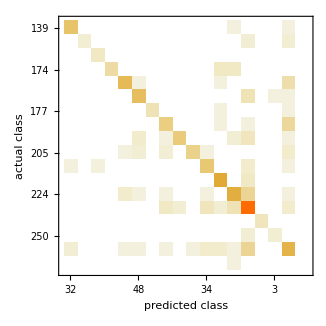

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
classifierData2=preprocessClassifierData[outOfCoreData,200,{64,64},Count[Flatten[ImageData[Binarize@Keys@#],1],0]≥(64*64)/6&&Length@classifier0[Keys@#,"TopProbabilities"]==1&];
```

```mathematica
Length@classifierData2
```

5957

```mathematica
classifierData2Training=Take[classifierData2,Floor[3Length@classifierData2/4]];
```

```mathematica
classifierData2Testing=Drop[classifierData2,Floor[3Length@classifierData2/4]];
```

```mathematica
RandomSample[classifierData2,40]
```

{-Graphics-→218,-Graphics-→226,-Graphics-→226,-Graphics-→218,-Graphics-→218,-Graphics-→224,-Graphics-→226,-Graphics-→217,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→203,-Graphics-→251,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→139,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→176,-Graphics-→226,-Graphics-→226,-Graphics-→218,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226,-Graphics-→226}

```mathematica
classifier1=Classify[classifierData2Training,ValidationSet->classifierData2Testing]
```

ClassifierFunction[…]

```mathematica
cm2=ClassifierMeasurements[classifier1,classifierData2Testing]
```

ClassifierMeasurementsObject[…]

```mathematica
cm2["Accuracy"]
```

0.965772

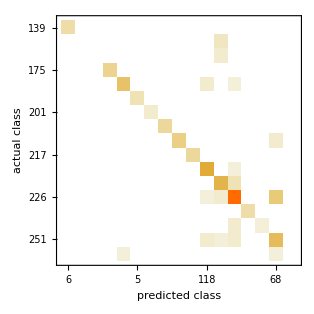

```mathematica
cm2["ConfusionMatrixPlot"]
```

## Trying it Out

```mathematica
samples=ImageResize[#,{512,128},Resampling->"Nearest"]&/@Import/@Keys@RandomSample[outOfCoreTestData,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
samples⟦1⟧
```

-Graphics-

```mathematica
reservedSample1
```

-Graphics-

```mathematica
reservedSample0
```

-Graphics-

```mathematica
seg=Binarize@trainedOutOfCore0[samples⟦1⟧]
```

-Graphics-

```mathematica
bboxes=Values@ComponentMeasurements[seg,"BoundingBox"]
```

{{{259.,90.},{264.,96.}},{{169.,87.},{176.,94.}},{{219.,86.},{226.,93.}},{{268.,87.},{274.,93.}},{{446.,89.},{448.,92.}},{{58.,84.},{64.,91.}},{{283.,82.},{289.,90.}},{{398.,85.},{401.,90.}},{{468.,83.},{474.,90.}},{{199.,82.},{204.,89.}},{{448.,87.},{450.,88.}},{{150.,79.},{155.,87.}},{{324.,80.},{329.,87.}},{{478.,80.},{484.,87.}},{{97.,80.},{103.,86.}},{{28.,42.},{39.,85.}},{{107.,77.},{112.,84.}},{{136.,77.},{142.,83.}},{{333.,77.},{338.,83.}},{{343.,78.},{346.,82.}},{{122.,73.},{127.,80.}},{{348.,74.},{355.,80.}},{{219.,70.},{225.,78.}},{{170.,70.},{175.,77.}},{{362.,71.},{368.,77.}},{{440.,65.},{444.,76.}},{{57.,67.},{63.,75.}},{{284.,67.},{289.,75.}},{{199.,68.},{204.,74.}},{{378.,68.},{384.,74.}},{{398.,67.},{404.,74.}},{{446.,67.},{452.,74.}},{{435.,52.},{439.,58.}},{{31.,0.},{36.,15.}},{{58.,7.},{63.,15.}},{{468.,7.},{473.,15.}},{{97.,7.},{103.,14.}},{{219.,7.},{225.,14.}},{{260.,7.},{265.,14.}},{{284.,8.},{289.,14.}},{{323.,7.},{329.,14.}},{{478.,1.},{483.,10.}},{{273.,0.},{276.,6.}},{{437.,0.},{441.,6.}},{{137.,0.},{143.,5.}},{{207.,0.},{212.,4.}},{{350.,0.},{355.,4.}},{{48.,1.},{49.,2.}}}

```mathematica
ShowBBoxes[samples⟦1⟧,Select[Rectangle@@#&/@bboxes,Area[#]≥25&]]
```

-Graphics-

```mathematica
images=First@ImageTrim[samples⟦1⟧,{Rectangle@@#},10]&/@Select[bboxes,Area[Rectangle@@#]≥25&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
resizedImages=ImageResize[ColorNegate@MorphologicalTransform[ColorNegate@Binarize@#,"Clean"],{64,64},Resampling->"Nearest"]&/@images
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
classified2=classifier/@resizedImages
```

{accidentalDoubleFlat,restQuarter,noteheadBlack,restQuarter,restQuarter,restQuarter,flag32ndUp,restQuarter,restQuarter,accidentalDoubleFlat,restQuarter,accidentalDoubleFlat,dynamicFF,restQuarter,restQuarter,restQuarter,restQuarter,restQuarter,restQuarter,restQuarter,restQuarter,flag16thUp,restQuarter,restQuarter,dynamicSforzando1,restQuarter,restQuarter,restQuarter,ornamentMordent,restQuarter,graceNoteAcciaccaturaStemUp,articTenutoAbove,articTenutoAbove,restQuarter,restQuarter,articTenutoAbove,restQuarter,fingering5}

```mathematica
Thread[{#1,#2}&[images,classified2]]//TableForm
```

-Graphics- | accidentalDoubleFlat
-Graphics- | restQuarter
-Graphics- | noteheadBlack
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | flag32ndUp
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | accidentalDoubleFlat
-Graphics- | restQuarter
-Graphics- | accidentalDoubleFlat
-Graphics- | dynamicFF
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | flag16thUp
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | dynamicSforzando1
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | ornamentMordent
-Graphics- | restQuarter
-Graphics- | graceNoteAcciaccaturaStemUp
-Graphics- | articTenutoAbove
-Graphics- | articTenutoAbove
-Graphics- | restQuarter
-Graphics- | restQuarter
-Graphics- | articTenutoAbove
-Graphics- | restQuarter
-Graphics- | fingering5

```mathematica
getClassified[inputImage_] := imageTakeRectangle[ImageResize[inputImage,{512,128},Resampling->"Nearest"],Rectangle@@#]&/@Values@ComponentMeasurements[Binarize@Blur@trainedOutOfCore0[ImageResize[inputImage,{512,128},Resampling->"Nearest"]],"BoundingBox"]
```

```mathematica
getClassified[samples⟦1⟧]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Staff Detection

## Finding the bottom of the staffs

TODO (pull from version 0.1)

## Finding the line distance

TODO (pull from version 0.1)

## Pitch Recognition

Pulled from version 0.1

```mathematica
PitchNumber[note_Rectangle,staffBottom_,δ_] := (RegionCentroid[note]⟦1⟧-staffBottom)/(0.5δ)
```

```mathematica
naturalNotes = Flatten[Table[#<>ToString[i]&/@{"A","B","C","D","E","F","G"},{i,1,7}],1]
```

{A1,B1,C1,D1,E1,F1,G1,A2,B2,C2,D2,E2,F2,G2,A3,B3,C3,D3,E3,F3,G3,A4,B4,C4,D4,E4,F4,G4,A5,B5,C5,D5,E5,F5,G5,A6,B6,C6,D6,E6,F6,G6,A7,B7,C7,D7,E7,F7,G7}

```mathematica
PitchToLetter[pitchNumber_,referenceNumber_,referenceLetter_] := RotateLeft[naturalNotes,FirstPosition[naturalNotes,referenceLetter]-1]⟦Round[pitchNumber-referenceNumber]+1⟧
```

## Parsing into Sheet Music

Current features:

Rhythm-less;

Accidental-less pitch detection;

Notes and chords;

Rests;

Articulations, matched to note groups;

```mathematica
BoxHeight[Rectangle[{_,starty_},{_,endy_}]] := endy-starty
```

```mathematica
staffTolerance=50
```

50

```mathematica
(*TODO*)
MusicOrder[ref_,staffs_][other_] := If[
Abs[RegionCentroid[ref["bbox"]]⟦1⟧-RegionCentroid[other["bbox"]]⟦1⟧]≤Median[BoxHeight/@staffs]+staffTolerance,
True,
RegionCentroid[ref["bbox"]]⟦0⟧<RegionCentroid[other["bbox"]]⟦0⟧
]
```

```mathematica
ParseSheetMusic[notes_,rests_,clefs_,articulations_,staffs_,δ_,ϵ_]:=(
clefPartitioned=SplitBy[notes,First[Sort[clefs,MusicOrder[#,staffs]]]&];(*TODO*)
pitchedNotes={};(*TODO*)
struct=SortBy[Join[
<|"type"->"notes","pitches"->(#["pitch"]&)/@#,"bbox"->First[#]|>&
/@Gather[pitchedNotes,Abs[RegionCentroid[#1["bbox"]]⟦0⟧-RegionCentroid[#2["bbox"]]⟦0⟧]≤ϵ&],
<|"type"->"rest","bbox"->#|>&
/@rests,
<|"type"->"clef","bbox"->#|>&
/@clefs
],
MusicOrder[#1,staffs][#2]&
];
articulationAssociations=AssociationMap[
articulation↦MinimalBy[Select[struct,#["type"]=="notes"],EuclideanDistance[RegionCentroid[#],RegionCentroid[articulation]]&],
articulations];
structure↦AssociateTo[structure,"articulations"->Keys[Select[articulationAssociations,structure==#&]]]/@struct
)
```